```mathematica
gammas14=Import["/Users/eug/Documents/research/hitchhikersscatter/code/tests/randomgamma1.4.txt","Table"];
```

```mathematica
Gamma`pc[y,a,a]//FullSimplify
```

(ⅇ^-y y^(-1+a))/Gamma[a]

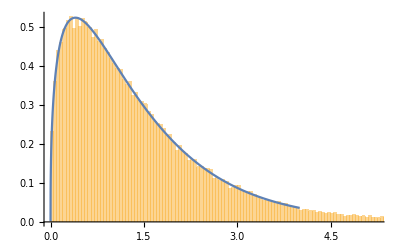

```mathematica
Show[
Histogram[gammas14,250,"PDF"
],
Plot[{(ⅇ^-y y^(-1+a))/Gamma[a]}/.a->1.4,{y,0,4},PlotRange->{0,6}]
]
```